```mathematica
datak1BL := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k1-1\\alice_varianceB0 BL.dat"][[All, {3,2,4}]]
datak1BR:= Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k1-1\\alice_varianceB0 BR.dat"][[All, {3,2,4}]]
datak1TL := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k1-1\\alice_varianceB0 TL.dat"][[All, {3,2,4}]]
datak1TR := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k1-1\\alice_varianceB0 TR.dat"][[All, {3,2,4}]]
datak2BL := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k2-2\\alice_varianceB0 BL.dat"][[All, {3,2,4}]]
datak2BR:= Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k2-2\\alice_varianceB0 BR.dat"][[All, {3,2,4}]]
datak2TL := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k2-2\\alice_varianceB0 TL.dat"][[All, {3,2,4}]]
datak2TR:= Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k2-2\\alice_varianceB0 TR.dat"][[All, {3,2,4}]]
```

```mathematica
datak1B:= Append[Flatten[datak1BL], Flatten[datak1BR]]
datak1T := Append[Flatten[datak1TL], Flatten[datak1TR]]
datak2B:=Append[Flatten[datak2BL], Flatten[datak2BR]]
datak2T:=Append[Flatten[datak2TL], Flatten[datak2TR]]
dataA := Append[datak1B, datak1T]
dataB := Append[datak2B, datak2T]
```

```mathematica
data := Partition[Flatten[dataA], 3]
data2 := Partition[Flatten[dataB], 3]
```

```mathematica
ListDensityPlot[data, InterpolationOrder->0, ColorFunction->"SunsetColors", PlotLegends->Automatic, PlotRange->All, FrameLabel->{λ,Γ},PlotLabel -> "Variance between rounds 6600 - 10000"]
ListDensityPlot[data2, InterpolationOrder->0, ColorFunction->"SunsetColors", PlotLegends->Automatic, PlotRange->All, FrameLabel->{λ,Γ},PlotLabel -> "Variance between rounds 6600 - 10000"]
```

-Graphics-

-Graphics-

```mathematica
dataChaos := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - work in progress\\alice_divergence0.dat"]
dataVariance :=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - work in progress\\k2 vs k2\\alice_variance0 b1.6-3.1.dat"]

bmin := 1.6
bmax := 3.1
```

```mathematica
ListDensityPlot[dataChaos, InterpolationOrder -> 0,PlotRange->{All,All, All},ColorFunction-> "SunsetColors", PlotLegends->Automatic]
```

-Graphics-

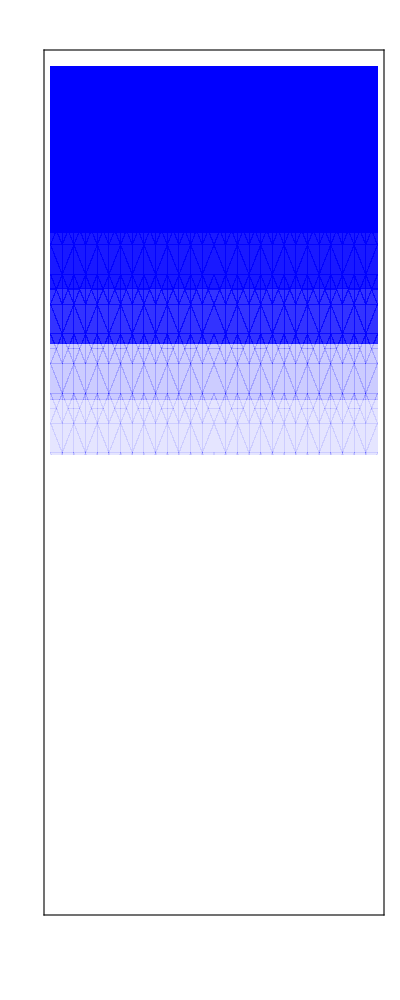

```mathematica
ContourPlot[y, {x, -0.1,0.1},{y,-0.5, 0.25}, Contours->{-0.1, -0.05, 0, 0.05, 0.1}, ContourShading->{None,{col, Opacity[0.1]}, {col, Opacity[0.2]}, {col, Opacity[0.8]},{col, Opacity[0.9]}, {col, Opacity[1]}}, ContourStyle->None, AspectRatio->5/2, FrameTicks->{{None,All}, {None, None}}, BaseStyle->{FontSize->26}]/.col->Blue
```

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\kLR notes files\\ContourLegend.png",%25,"PNG", ImageResolution->200]
```

D:\Users\User\Dropbox\Dropbox\MPhys Project\kLR notes files\ContourLegend.png

```mathematica
ListContourPlot[dataChaos, PlotRange->All, Contours->{-0.1, -0.05, 0, 0.05, 0.1}, ContourShading->{None,{col, Opacity[0.1]}, {col, Opacity[0.2]}, {col, Opacity[0.8]},{col, Opacity[0.9]}, {col, Opacity[1]}}, ContourStyle->None]/.col->Blue
```

-Graphics-

```mathematica
Show[%9,%8, FrameLabel->{β,λ}]
```

-Graphics-

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\kLR notes files\\RPSContour.png", %11, "PNG", ImageResolution->200]
```

D:\Users\User\Dropbox\Dropbox\MPhys Project\kLR notes files\RPSContour.png

```mathematica
ListDensityPlot[dataVariance, InterpolationOrder -> 1, PlotRange->{All,All, Automatic}, ColorFunction-> "SunsetColors", PlotLegends->Automatic]
```

-Graphics-